# Runtime Testing

```mathematica
<<CRNSSA`
```

rxn::shdw: Symbol rxn appears in multiple contexts {CRNSSA`,CRNSimulator`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

revrxn::shdw: Symbol revrxn appears in multiple contexts {CRNSSA`,CRNSimulator`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

init::shdw: Symbol init appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

GetSpecies::shdw: Symbol GetSpecies appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

DirectSSA::shdw: Symbol DirectSSA appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

```mathematica
ConstructSys1[n_,type_]:=Module[
{rxns,xInits,yInits,inits},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xInits=Table[type[x[i],RandomInteger[100]],{i,n}];
yInits=Table[type[y[i],RandomInteger[100]],{i,n}];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys2[n_,type_]:=Module[
{k,rxns,xInits,yInits,inits},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[x[i]+x[j],y[i,j],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xInits=Table[type[x[i],RandomInteger[100]],{i,k}];
yInits=Flatten[Table[type[y[i,j],RandomInteger[100]],{i,k},{j,k}]];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys3[n_,type_]:=Module[
{rxns,inits},
rxns= Table[revrxn[x,y,RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
inits={type[x,RandomInteger[100]],type[y,RandomInteger[100]]};
{rxns,inits}]
```

```mathematica
TestSys[construction_,algo_,kRange_,iters_]:=Module[{type},
If[algo==="Opt",type=init,type=conc];
Table[Module[
{n,rxns,inits,rxnsys,nRxns,nSpecies,results,time,nIters,timePerIter},
n=k^2;
{rxns,inits} = construction[n,type];
rxnsys=Flatten[{rxns,inits}];
nRxns=Length[rxns];
nSpecies=If[algo==="Opt",
Length[GetSpecies[rxnsys]],
Length[SpeciesInRxnsys[rxnsys]]];
results=If[algo==="Opt",
Timing[DirectSSA[rxnsys,"useIter"->True,"iterEnd"->iters]],
Timing[SimulateRxnsysSSA[rxnsys,1/n]]];
time=results[[1]];
nIters=If[algo==="Opt",
iters,
Length[Normal[results[[2]]]]];
timePerIter=time/nIters;
{nRxns,nSpecies,time,nIters,timePerIter}],
kRange]]
```

```mathematica
algo="Opt";
kRange={k,1,25,4};
iters=1000;
resultsOpt1=TestSys[ConstructSys1,algo,kRange,iters];
resultsOpt2=TestSys[ConstructSys2,algo,kRange,iters];
resultsOpt3=TestSys[ConstructSys3,algo,kRange,iters];
```

```mathematica
resultsOpt1
resultsOpt2
resultsOpt3
```

{{2,2,0.,1000,0.},{50,50,0.03125,1000,0.00003125},{162,162,0.109375,1000,0.000109375},{338,338,0.453125,1000,0.000453125},{578,578,1.125,1000,0.001125},{882,882,2.35938,1000,0.00235938},{1250,1250,4.8125,1000,0.0048125}}

{{2,2,0.,1000,0.},{50,30,0.03125,1000,0.00003125},{162,90,0.09375,1000,0.00009375},{338,182,0.328125,1000,0.000328125},{578,306,0.796875,1000,0.000796875},{882,462,1.71875,1000,0.00171875},{1250,650,3.54688,1000,0.00354688}}

{{2,2,0.015625,1000,0.000015625},{50,2,0.03125,1000,0.00003125},{162,2,0.078125,1000,0.000078125},{338,2,0.21875,1000,0.00021875},{578,2,0.390625,1000,0.000390625},{882,2,0.734375,1000,0.000734375},{1250,2,1.15625,1000,0.00115625}}

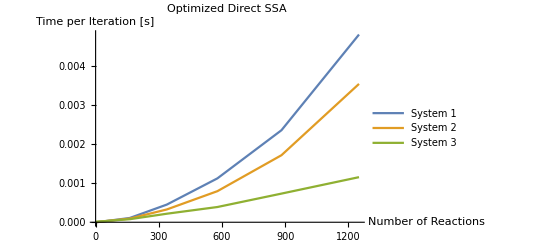

```mathematica
coorsOpt1nRxn=Table[{resultsOpt1[[i]][[1]],resultsOpt1[[i]][[5]]},{i,Length[resultsOpt1]}];
coorsOpt2nRxn=Table[{resultsOpt2[[i]][[1]],resultsOpt2[[i]][[5]]},{i,Length[resultsOpt2]}];
coorsOpt3nRxn=Table[{resultsOpt3[[i]][[1]],resultsOpt3[[i]][[5]]},{i,Length[resultsOpt3]}];
ListLinePlot[{coorsOpt1nRxn,coorsOpt2nRxn,coorsOpt3nRxn},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA"]
```

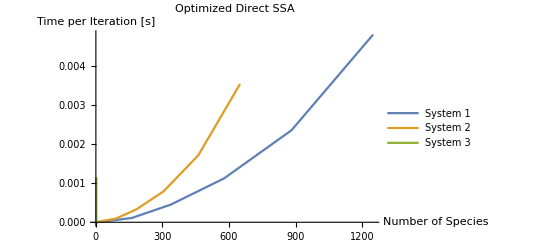

```mathematica
coorsOpt1nSpc=Table[{resultsOpt1[[i]][[2]],resultsOpt1[[i]][[5]]},{i,Length[resultsOpt1]}];
coorsOpt2nSpc=Table[{resultsOpt2[[i]][[2]],resultsOpt2[[i]][[5]]},{i,Length[resultsOpt2]}];
coorsOpt3nSpc=Table[{resultsOpt3[[i]][[2]],resultsOpt3[[i]][[5]]},{i,Length[resultsOpt3]}];
ListLinePlot[{coorsOpt1nSpc,coorsOpt2nSpc,coorsOpt3nSpc},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Species","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA"]
```

```mathematica
<<CRNSimulatorSSA`
```

```mathematica
algo="Naive";
kRange={k,1,25,4};
iters=1000;
resultsNaive1=TestSys[ConstructSys1,algo,kRange,iters];
resultsNaive2=TestSys[ConstructSys2,algo,kRange,iters];
resultsNaive3=TestSys[ConstructSys3,algo,kRange,iters];
```

```mathematica
resultsNaive1
resultsNaive2
resultsNaive3
```

{{2,2,0.265625,270,0.000983796},{50,50,0.875,595,0.00147059},{162,162,2.46875,545,0.00452982},{338,338,5.625,500,0.01125},{578,578,9.875,576,0.0171441},{882,882,15.9844,597,0.0267745},{1250,1250,24.0938,518,0.046513}}

{{2,2,0.171875,1871,0.0000918626},{50,30,1.07813,543,0.0019855},{162,90,3.48438,734,0.0047471},{338,182,7.09375,810,0.00875772},{578,306,12.875,943,0.0136532},{882,462,19.2969,1105,0.0174632},{1250,650,28.6875,1137,0.0252309}}

{{2,2,0.140625,216,0.000651042},{50,2,0.796875,421,0.00189281},{162,2,2.32813,368,0.00632643},{338,2,4.42188,61,0.0724898},{578,2,7.4375,467,0.0159261},{882,2,11.1875,165,0.067803},{1250,2,16.0938,343,0.0469206}}

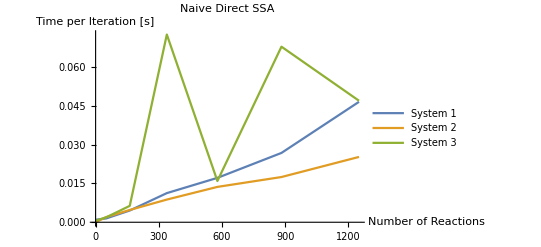

```mathematica
coorsNaive1nRxn=Table[{resultsNaive1[[i]][[1]],resultsNaive1[[i]][[5]]},{i,Length[resultsNaive1]}];
coorsNaive2nRxn=Table[{resultsNaive2[[i]][[1]],resultsNaive2[[i]][[5]]},{i,Length[resultsNaive2]}];
coorsNaive3nRxn=Table[{resultsNaive3[[i]][[1]],resultsNaive3[[i]][[5]]},{i,Length[resultsNaive3]}];
ListLinePlot[{coorsNaive1nRxn,coorsNaive2nRxn,coorsNaive3nRxn},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Naive Direct SSA"]
```

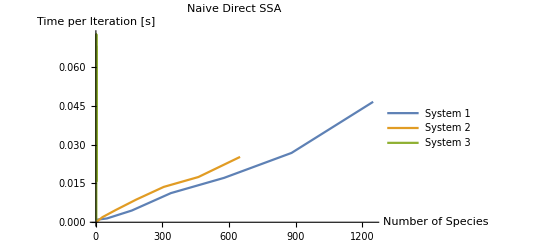

```mathematica
coorsNaive1nSpc=Table[{resultsNaive1[[i]][[2]],resultsNaive1[[i]][[5]]},{i,Length[resultsNaive1]}];
coorsNaive2nSpc=Table[{resultsNaive2[[i]][[2]],resultsNaive2[[i]][[5]]},{i,Length[resultsNaive2]}];
coorsNaive3nSpc=Table[{resultsNaive3[[i]][[2]],resultsNaive3[[i]][[5]]},{i,Length[resultsNaive3]}];
ListLinePlot[{coorsNaive1nSpc,coorsNaive2nSpc,coorsNaive3nSpc},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Species","Time per Iteration [s]"},"PlotLabel"->"Naive Direct SSA"]
```

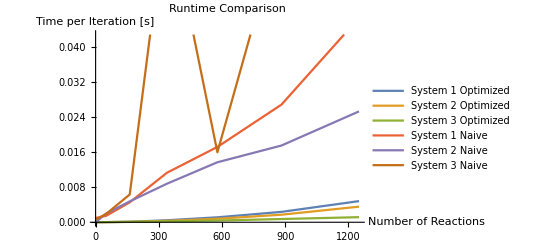

```mathematica
ListLinePlot[{coorsOpt1nRxn,coorsOpt2nRxn,coorsOpt3nRxn,coorsNaive1nRxn,coorsNaive2nRxn,coorsNaive3nRxn},PlotLegends->{"System 1 Optimized","System 2 Optimized","System 3 Optimized","System 1 Naive","System 2 Naive","System 3 Naive"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Runtime Comparison"]
```

```mathematica
(*resultsNaive=Table[Module[{rxns= Flatten[Table[revrxn[x[i]+x[j],y[i,j],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]],
xInits=Table[conc[x[i],RandomInteger[100]],{i,k}],
yInits=Flatten[Table[conc[y[i,j],RandomInteger[100]],{i,k},{j,k}]],
rxnsys,results,nRxns,time,iters,timePerIter},
rxnsys = Flatten[{rxns,xInits,yInits}];
results=Timing[SimulateRxnsysSSA[rxnsys,100/(k^2)]];
nRxns=Length[rxns];
time=results[[1]];
iters=Length[Normal[results[[2]]]];
timePerIter=time/iters;
{nRxns,time,iters,timePerIter}],
{k,1,9,4}]*)
```

{{2,0.21875,32336,6.76491×10^-6},{32,1.10938,32853,0.0000337678}}